```mathematica
Nt = 647; 
ti = 0; tf = 5; 
deltat = (tf - ti) /Nt ;
Nx = 455;
xi = -40; xf = 40; 
deltax = (xf - xi) / Nx; 
c =  1;

(*For Max Eigenvalue Plots*)
rs = N[Table[0.1*i,{i,1,20}],32];

maxevalsLD2 = N[Table[0,{i,1,Length[rs]}],32];
maxevalsRK2 = N[Table[0,{i,1,Length[rs]}],32];
maxevalsPI = N[Table[0,{i,1,Length[rs]}],32];
difference = N[Table[0,{i,1,Length[rs]}],32];



Subscript[δ, i_,j_]:=KroneckerDelta[i,j];

selectwidth = 8;
diffOrder = 2;
deriv = 2;


(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

(*Set up the grid for the stencil*)
grid= x0+(Range[totalpoints]-middlepoint)Δx;

(LP=NDSolve`FiniteDifferenceDerivative[Derivative[deriv],grid,"DifferenceOrder"->diffOrder]@"DifferentiationMatrix"//Normal);

(*define r:=Δt/(Δx^deriv)*)
r=.;
LPX = LP*((-1)^deriv)*(r*(Δx)^deriv);

gn = (LPX[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX = Table[RotateRight[gn,i],{i,-selectwidth,selectwidth}];

IP=IdentityMatrix[Length[LPX]];

(Mn=N[Inverse[IP-(ⅈ * LPX)/4 ].(IP+(ⅈ * LPX)/4),32]);

fn=N[(Mn[[middlepoint,All]]//Normal)//Simplify//FullSimplify,32];


(*Generate a M Matrix from the L matrix for the stencil*)
MP = N[Table[0,{i,1,Nx},{j,1,Nx}],32];



(*WITH Periodic Boundary Conditions*)
MP = N[Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fn[[selectwidth - n]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fn[[(middlepoint + 1) + n]]  ,{n,0,selectwidth - 1}],{i,0,Nx-1},{j,0,Nx-1}],32];
```

```mathematica
Do[
deltat = N[(deltax^2) * rs[[p]],32];

Xp= N[Table[xm = xi + m *deltax, {m, 0, Nx}],32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

f[x_] = ⅇ^(- x^2+ⅈ x);


(************************************************************************************************************************)
(*Differentiation Matrix*)
(************************************************************************************************************************)
L1 = N[(NDSolve`FiniteDifferenceDerivative[Derivative[1],Xp,"DifferenceOrder"->1, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal),32];
L1//MatrixForm;
DL1 = N[-c * L1 * deltat,32];

L2 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],Xp, "DifferenceOrder"->2, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal), {i,1,8}],32];
(*DL2 = N[Table[L2[[i]] * (deltat)^(i),{i,2,8}],32];*)
DL2 = N[L2[[2]] * deltat * (ⅈ / 2),32];
DL4 = L2[[4]] * (deltat * (ⅈ / 2))^2;
DL6 = L2[[6]] * (deltat * (ⅈ / 2))^3;
DL8 = L2[[8]] * (deltat * (ⅈ / 2))^4;


(* LD2 *)
ILD2 = N[IdentityMatrix[Length[DL2]],32];
ALD2 = N[ILD2 - (DL2 / 2),32];
BLD2 = N[ILD2 + (DL2 / 2),32];
MLD2 = N[Inverse[ALD2].BLD2,32];

evals = Eigenvalues[N[MLD2]];
realEvalsLD2 = Re[evals];
imagEvalsLD2 = Im[evals];

maxevalsLD2[[p]] = Max[Abs[evals]];



(*RK2*)
IRK2 = N[IdentityMatrix[Length[DL2]],32];

MRK2 = N[(IRK2 + (DL2) + ((1/2)*(DL4))) +  ((1/6) * (DL6)),32];

evalsRK2 = Eigenvalues[N[MRK2]];
realEvalsRK2 = Re[evalsRK2];
imagEvalsRK2 = Im[evalsRK2];

maxevalsRK2[[p]] = Max[Abs[evalsRK2]];

(*PI*)

MPtest = N[MP//.{N[r -> deltat / (deltax)^2,32]},32];


(*Generate a M Matrix from the L matrix for the stencil*)
MCompare = N[Table[0,{i,1,Nx},{j,1,Nx}],32];

fcompare = N[fn//.{r -> (deltat / (deltax)^2)},32];

(*WITH Periodic Boundary Conditions*)
MCompare = N[Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fcompare[[k]] + (Subscript[δ, i,(j-k)])fcompare[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fcompare[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fcompare[[selectwidth - n]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fcompare[[(middlepoint + 1) + n]]  ,{n,0,selectwidth - 1}],{i,0,Nx-1},{j,0,Nx-1}],32];

  

(*difference[[p]] = Max[MCompare - MPtest];*)

evalsPI = N[Eigenvalues[N[MPtest,32]],32];
evalsCompare = N[Eigenvalues[N[MCompare,32]],32];
difference[[p]] = Max[evalsPI - evalsCompare];
realEvalsPI = Re[evalsPI];
imagEvalsPI = Im[evalsPI];

maxevalsPI[[p]] = N[Max[Abs[evalsPI]],32];


Print["Finished "<>ToString[rs[[p]]]];


,{p,1,Length[rs]}]


(*For Max Eigenvalue Plots*)
(*exportData=Flatten/@Transpose[{rsLD2,maxevalsLD2,rsEuler, maxevalsEuler, rsRK2, maxevalsRK2, rsRK4, maxevalsRK4, rsN, maxevalsN}];*)
(*Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_max.dat",exportData,"Table"];*)
```

Finished 0.1

Finished 0.2

Finished 0.3

Finished 0.4

Finished 0.5

Finished 0.6

Finished 0.7

Finished 0.8

Finished 0.9

Finished 1.

Finished 1.1

Finished 1.2

Finished 1.3

Finished 1.4

Finished 1.5

Finished 1.6

Finished 1.7

Finished 1.8

Finished 1.9

Finished 2.

```mathematica
maxevalsLD2 = Join[{1},maxevalsLD2];
rsLD2 = Join[{0},rs];

maxevalsRK2 = Join[{1},maxevalsRK2];
rsRK2 = Join[{0},rs];

maxevalsPI = Join[{1},maxevalsPI];
rsPI = Join[{0},rs];
```

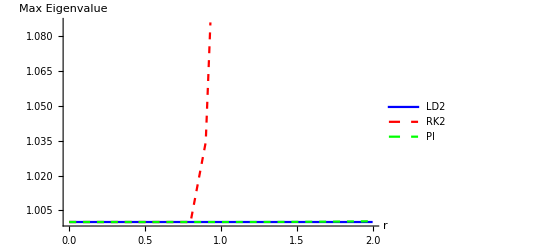

```mathematica
ListLinePlot[{Transpose[{rsLD2,maxevalsLD2}],Transpose[{rsRK2,maxevalsRK2}],Transpose[{rsPI,maxevalsPI}]},PlotStyle->{Blue,{Red, Dashed}, {Green, Dashed}}, PlotLegends->{"LD2", "RK2", "PI"}, AxesLabel->{"r", "Max Eigenvalue"}]
```

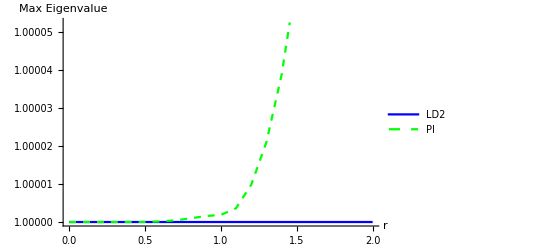

```mathematica
ListLinePlot[{Transpose[{rsLD2,maxevalsLD2}],Transpose[{rsPI,maxevalsPI}]},PlotStyle->{Blue, {Green, Dashed}}, PlotLegends->{"LD2", "PI"}, AxesLabel->{"r", "Max Eigenvalue"}]
```

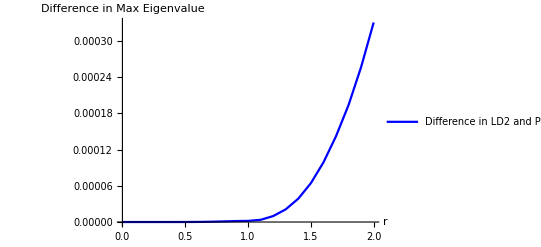

```mathematica
ListLinePlot[{Transpose[{rsLD2,Abs[maxevalsLD2 - maxevalsPI]}]},PlotStyle->{Blue}, PlotLegends->{"Difference in LD2 and PI"}, AxesLabel->{"r", "Difference in Max Eigenvalue"}]
```

```mathematica
Abs[maxevalsLD2 - maxevalsPI]
```

{0,2.22045×10^-15,8.58869×10^-12,4.07517×10^-10,5.52937×10^-9,3.67013×10^-8,1.51308×10^-7,4.38563×10^-7,9.52948×10^-7,1.57868×10^-6,1.87028×10^-6,3.62929×10^-6,9.82518×10^-6,0.0000209705,0.0000386613,0.0000642451,0.000098581,0.000141874,0.000193586,0.000256439,0.000330284}

```mathematica
MPtest[[1,1]]
```

0.137729-0.703155 ⅈ

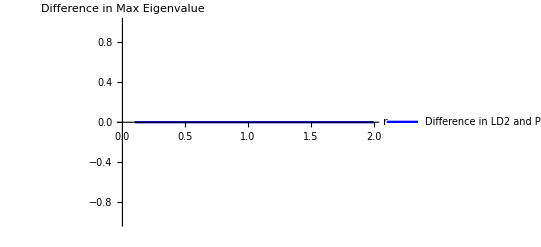

```mathematica
ListLinePlot[{Transpose[{rs,difference}]},PlotStyle->{Blue}, PlotLegends->{"Difference in LD2 and PI"}, AxesLabel->{"r", "Difference in Max Eigenvalue"}]
```

```mathematica
difference
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}